## Define Models, Give Basic Example

```mathematica
(* Defining parameters *)
poppars={n1->500.,n2->500.};
PRpars = {PR1 -> 0.1, PR2->.05};
(* Aligning Movement parameters *)
tarpars= {ϕ1->1/5., τ12 ->1/3.,ϕ2->1/20.,τ21 ->1/3.};
movtar ={0 == - ϕ1 n11 + τ12 n12,
0 == - ϕ2 n22+ τ21  n21,
(* Normalize to the residence populations *)
n11 + n12 == n1,
n22 + n21 == n2
};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]];
mtar ={m12-> (τ12 ϕ1)/(τ12+ϕ1)n1+(τ21 ϕ2)/(τ21+ϕ2)n2,m21->(τ12 ϕ1)/(τ12+ϕ1)n1+(τ21 ϕ2)/(τ21+ϕ2)n2};
fluxpars ={f12->(m12/n1),f21->(m21/n2)}/.mtar/.tarpars/.poppars;
RMpars = {a->.27,c->.15,g->.1,r->1/200.};
```

```mathematica
(* This is the TaR Ross-Macdonald Model *)
ψ ={{τ12/(τ12 + ϕ1),ϕ1/(τ12 + ϕ1)},{ϕ2/(τ21 + ϕ2),τ21/(τ12 + ϕ2)}};
Transpose[ψ].{n1,n2};
κ[PR1_,PR2_]:=  Transpose[ψ].{PR1*n1,PR2*n2}/Transpose[ψ].{n1,n2};
RTaR[PR1_,PR2_]:=Inverse[ψ].({PR1,PR2}/{(1-PR1),(1-PR2)})/(κ[PR1,PR2]/(1 + (a c)/g κ[PR1,PR2]))
```

```mathematica
(* First example of solving the TaR Ross-Macdonald Model *)
Inverse[ψ].({PR1,PR2}/{(1-PR1),(1-PR2)})/(κ[PR1,PR2]/(1 + (a c)/g κ[PR1,PR2]))/.PRpars/.tarpars/.RMpars/.poppars
```

{1.16781,1.05169}

```mathematica
RTaR[.1,.05]/.tarpars/.poppars/.RMpars
```

{1.16781,1.05169}

```mathematica
(* This is the Flux Model *)
RFlux[PR1_,PR2_]:=(r* {PR1,PR2}+({ f12*PR1 -f21*PR2 ,f21 PR2 - f12 PR1}))/{1-PR1, 1-PR2}/((r {PR1,PR2})/(1 +(a c)/g{PR1,PR2}))
```

```mathematica
(* First example of solving the Flux Ross-Macdonald Model *)
RFlux[PR1,PR2]/.PRpars/.fluxpars/.tarpars/.RMpars
```

{20.6341,-35.1134}

#### Test example : no travel

```mathematica
tarpars= {ϕ1->0., τ12 ->1/3.,ϕ2->0.,τ21 ->1/3.};
fluxpars ={f12->(m12/n1),f21->(m21/n2)}/.mtar/.tarpars/.poppars;
```

```mathematica
RTaR[PR1,PR2]/.{PR1->.25,PR2->.25}/.tarpars/.poppars/.RMpars

-(g+a c PR1)/(g (-1+PR1))/.RMparams/.PR1->.25
```

{1.46833,1.46833}

1.46833

```mathematica
RFlux[PR1,PR2]/.{PR1->.25,PR2->.25}/.fluxpars/.tarpars/.poppars/.RMpars
```

{1.46833,1.46833}

#### Another example : travel, but with zero PR in one of the locations

```mathematica
tarpars= {ϕ1->1/1000., τ12 ->1/10.,ϕ2->1/10000.,τ21 ->1/10.};
fluxpars ={f12->(m12/n1),f21->(m21/n2)}/.mtar/.tarpars/.poppars;
```

```mathematica
ψ/.tarpars
κ[PR1,PR2]/.{PR1->.25,PR2->0.02}/.tarpars/.poppars

fluxpars/.tarpars
```

{{0.990099,0.00990099},{0.00990099,0.990099}}

{0.247723,0.0222772}

{f12→0.0019802,f21→0.0019802}

```mathematica
Table[Flatten[{
X,
RTaR[PR1,PR2]/.{PR1->X,PR2->0.05}/.RMpars/.tarpars/.poppars,
-(g+a c PR1)/(g (-1+PR1))/.RMparams/.PR1->X
}],{X,0.01,.5,.01}]
```

{{0.01,0.934214,1.09119,1.01419},{0.02,0.997573,1.08692,1.02867},{0.03,1.02934,1.08262,1.04345},{0.04,1.05316,1.0783,1.05854},{0.05,1.07395,1.07395,1.07395},{0.06,1.09337,1.06956,1.08968},{0.07,1.11217,1.06515,1.10575},{0.08,1.13072,1.0607,1.12217},{0.09,1.14922,1.05621,1.13896},{0.1,1.16781,1.05169,1.15611},{0.11,1.18659,1.04713,1.17365},{0.12,1.20562,1.04253,1.19159},{0.13,1.22495,1.03789,1.20994},{0.14,1.24462,1.0332,1.22872},{0.15,1.26466,1.02847,1.24794},{0.16,1.2851,1.02369,1.26762},{0.17,1.30598,1.01886,1.28777},{0.18,1.32731,1.01398,1.30841},{0.19,1.34913,1.00905,1.32957},{0.2,1.37145,1.00405,1.35125},{0.21,1.39431,0.999002,1.37348},{0.22,1.41772,0.99389,1.39628},{0.23,1.44171,0.988712,1.41968},{0.24,1.46632,0.983467,1.44368},{0.25,1.49156,0.978152,1.46833},{0.26,1.51746,0.972762,1.49365},{0.27,1.54406,0.967295,1.51966},{0.28,1.57138,0.961747,1.54639},{0.29,1.59946,0.956114,1.57387},{0.3,1.62833,0.950392,1.60214},{0.31,1.65802,0.944577,1.63123},{0.32,1.68858,0.938664,1.66118},{0.33,1.72004,0.932649,1.69201},{0.34,1.75244,0.926526,1.72379},{0.35,1.78584,0.92029,1.75654},{0.36,1.82026,0.913935,1.79031},{0.37,1.85578,0.907456,1.82516},{0.38,1.89243,0.900845,1.86113},{0.39,1.93028,0.894096,1.89828},{0.4,1.96939,0.887202,1.93667},{0.41,2.00981,0.880154,1.97636},{0.42,2.05162,0.872945,2.01741},{0.43,2.0949,0.865564,2.05991},{0.44,2.13972,0.858004,2.10393},{0.45,2.18616,0.850253,2.14955},{0.46,2.23432,0.8423,2.19685},{0.47,2.28429,0.834133,2.24594},{0.48,2.33618,0.82574,2.29692},{0.49,2.3901,0.817107,2.3499},{0.5,2.44617,0.808219,2.405}}

```mathematica
RFlux[PR1,PR2]/.{PR1->.01,PR2->0.05}/.fluxpars/.tarpars/.poppars/.RMpars
```

{-0.592449,1.41421}

```mathematica
Table[Flatten[{
X,
RFlux[PR1,PR2]/.{PR1->X,PR2->0.05}/.fluxpars/.tarpars/.poppars/.RMpars,
-(g+a c PR1)/(g (-1+PR1))/.RMparams/.PR1->X
}],{X,0.01,.5,.01}]
```

{{0.01,0.129817,1.26124,1.01419},{0.02,0.692298,1.21442,1.02867},{0.03,0.891805,1.1676,1.04345},{0.04,1.00085,1.12077,1.05854},{0.05,1.07395,1.07395,1.07395},{0.06,1.12927,1.02712,1.08968},{0.07,1.17463,0.980299,1.10575},{0.08,1.21391,0.933475,1.12217},{0.09,1.24931,0.886651,1.13896},{0.1,1.28213,0.839827,1.15611},{0.11,1.31321,0.793003,1.17365},{0.12,1.34312,0.746179,1.19159},{0.13,1.37226,0.699355,1.20994},{0.14,1.40092,0.652531,1.22872},{0.15,1.42931,0.605707,1.24794},{0.16,1.4576,0.558883,1.26762},{0.17,1.48594,0.512059,1.28777},{0.18,1.51442,0.465234,1.30841},{0.19,1.54314,0.41841,1.32957},{0.2,1.57218,0.371586,1.35125},{0.21,1.60161,0.324762,1.37348},{0.22,1.63149,0.277938,1.39628},{0.23,1.66188,0.231114,1.41968},{0.24,1.69284,0.18429,1.44368},{0.25,1.72441,0.137466,1.46833},{0.26,1.75665,0.090642,1.49365},{0.27,1.78959,0.0438179,1.51966},{0.28,1.8233,-0.00300617,1.54639},{0.29,1.85782,-0.0498302,1.57387},{0.3,1.8932,-0.0966543,1.60214},{0.31,1.92948,-0.143478,1.63123},{0.32,1.96673,-0.190302,1.66118},{0.33,2.00499,-0.237127,1.69201},{0.34,2.04431,-0.283951,1.72379},{0.35,2.08476,-0.330775,1.75654},{0.36,2.12639,-0.377599,1.79031},{0.37,2.16927,-0.424423,1.82516},{0.38,2.21347,-0.471247,1.86113},{0.39,2.25905,-0.518071,1.89828},{0.4,2.30609,-0.564895,1.93667},{0.41,2.35466,-0.611719,1.97636},{0.42,2.40485,-0.658543,2.01741},{0.43,2.45676,-0.705367,2.05991},{0.44,2.51046,-0.752191,2.10393},{0.45,2.56608,-0.799015,2.14955},{0.46,2.62371,-0.845839,2.19685},{0.47,2.68347,-0.892663,2.24594},{0.48,2.74549,-0.939488,2.29692},{0.49,2.80991,-0.986312,2.3499},{0.5,2.87686,-1.03314,2.405}}

```mathematica
RFlux[PR1,PR2]/.{PR1->.25,PR2->.25}/.tarpars/.poppars/.RMpars
```

# (Upper Left) High Freq Travel; High L2 PR

```mathematica
tarpars= {ϕ1->1/360, τ12 ->1/10,ϕ2->1/360,τ21 ->1/10};
fluxpars ={f12->(m12/n1),f21->(m21/n2)}/.mtar/.tarpars/.poppars;
PRpars={PR1->X,PR2->.25}; (*High transmission in location 2*)
```

```mathematica
RTaR[.04,.3]/.RMpars/.tarpars/.poppars
RFlux[.04,.3]/.RMpars/.fluxpars/.tarpars/.poppars
```

{0.663348,1.67862}

{-742.782,151.713}

```mathematica
datFastHigh = Table[Flatten[{
X,
RTaR[X,PR2][[1]]/.PRpars/.RMpars/.tarpars/.poppars,
RFlux[X,PR2][[1]]/.PRpars/.RMpars/.fluxpars/.tarpars/.poppars}],
{X,0.01,.5,.01}];
```

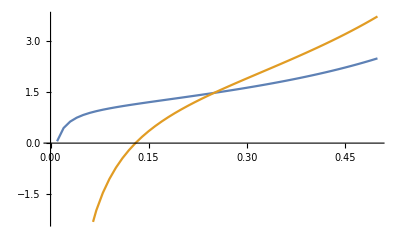

```mathematica
ListLinePlot[{datFastHigh[[;;,{1,2}]],datFastHigh[[;;,{1,3}]]}]
```

# (Upper Right) High Freq Travel; Low L2 PR

```mathematica
tarpars= {ϕ1->1/360., τ12 ->1/10.,ϕ2->1/360.,τ21 ->1/10.};
fluxpars ={f12->(m12/n1),f21->(m21/n2)}/.mtar/.tarpars/.poppars;
PRpars={PR1->X,PR2->.025}; (*High transmission in location 2*)
```

```mathematica
RTaR[.04,.3]/.RMpars/.tarpars/.poppars
RFlux[.04,.3]/.RMpars/.fluxpars/.tarpars/.poppars
```

{0.359857,1.75913}

{-13.4268,4.52535}

```mathematica
datFastLow = Table[Flatten[{
X,
RTaR[X,PR2][[1]]/.PRpars/.RMpars/.tarpars/.poppars,
RFlux[X,PR2][[1]]/.PRpars/.RMpars/.fluxpars/.tarpars/.poppars}],
{X,0.01,.5,.01}];
```

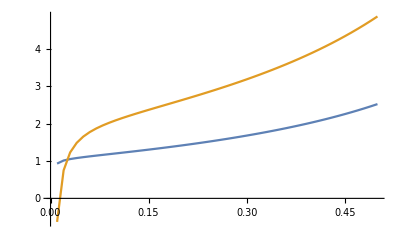

```mathematica
ListLinePlot[{datFastLow[[;;,{1,2}]],datFastLow[[;;,{1,3}]]}]
```

# (Lower Left) Low Freq Travel; High L2 PR

```mathematica
tarpars= {ϕ1->1/36000., τ12 ->1/1000,ϕ2->1/36000.,τ21 ->1/1000};
fluxpars ={f12->(m12/n1),f21->(m21/n2)}/.mtar/.tarpars/.poppars;
PRpars={PR1->X,PR2->.25}; (*High transmission in location 2*)
```

```mathematica
RTaR[.04,.3]/.RMpars/.tarpars/.poppars
RFlux[.04,.3]/.RMpars/.fluxpars/.tarpars/.poppars
```

{1.01321,1.60962}

{0.296157,1.756}

```mathematica
datSlowHigh= Table[Flatten[{
X,
RTaR[X,PR2][[1]]/.PRpars/.RMpars/.tarpars/.poppars,
RFlux[X,PR2][[1]]/.PRpars/.RMpars/.fluxpars/.tarpars/.poppars}],
{X,0.01,.5,.01}];
```

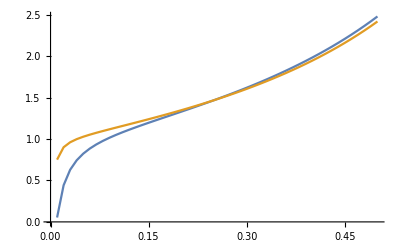

```mathematica
ListLinePlot[{datSlowHigh[[;;,{1,2}]],datSlowHigh[[;;,{1,3}]]}]
```

# (Lower Right) High Freq Travel; Low L2 PR

```mathematica
tarpars= {ϕ1->1/36000., τ12 ->1/1000,ϕ2->1/36000.,τ21 ->1/1000};
fluxpars ={f12->(m12/n1),f21->(m21/n2)}/.mtar/.tarpars/.poppars;
PRpars={PR1->X,PR2->.025}; (*High transmission in location 2*)
```

```mathematica
RTaR[.04,.3]/.RMpars/.tarpars/.poppars
RFlux[.04,.3]/.RMpars/.fluxpars/.tarpars/.poppars
```

{0.663348,1.67862}

{-6.37986,3.10325}

```mathematica
datSlowLow = Table[Flatten[{
X,
RTaR[X,PR2][[1]]/.PRpars/.RMpars/.tarpars/.poppars,
RFlux[X,PR2][[1]]/.PRpars/.RMpars/.fluxpars/.tarpars/.poppars}],
{X,0.01,.5,.01}];
```

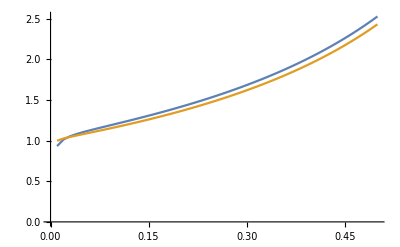

```mathematica
ListLinePlot[{datSlowLow[[;;,{1,2}]],datSlowLow[[;;,{1,3}]]}]
```